Reaching high laser intensity by a radiating electron

M. Jirka, et al, Phys. Rev. A 103, 053114
Notebook: Óscar Amaro, June 2021/Jan 2022 @ GoLP-EPP

Figure 1
Problem: what is the definition of T(τ)? By inspection it’s possible to determine an approximate relation, though it does not seem to be explicit in the text.

(47/63)^((0.0301991 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)) ℰe

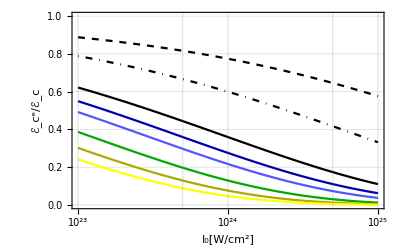

```mathematica
Clear[χe,ℰe,γe,Wγ,pc,tc,ω0,E0,ℰc,me,c,e,α,ℏ,T,ES,λμm,τ]

χe=2γe E0/ES;
γe=ℰe/(me c^2);
Wγ=3^(2/3) 28 Gamma[2/3] α me^2 c^4χe^(2/3)  /(54 ℏ ℰe) ;
pc = Wγ tc;
tc=τ/(2Sqrt[2Log[2]]);
ω0=2π c/(λμm 10^-6);
E0=0.855 λμm  Sqrt[I0 10^-18] me ω0 c/e;


ℰc=(1-16/63)^pc  ℰe (*Refine[//Simplify,{c>0,me>0,E0>0,ES>0,ℏ>0,ℰe>0,τ>0}]//FullSimplify*)


me=9.11 10^-31;(*[Kg]*)
c= 299792458; (*[m/s]*)
e=1.602176634 10^-19; (*[C]*)
α=1/137; (*[]*)
ℏ=1.054571817 10^-34;(*[J s]*)
T=0.67(λμm 10^-6)/c;
ES=me^2 c^3/(e ℏ);(*[V/m]*)

LogLinearPlot[{((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->100 10^9 e,τ->T,λμm->0.25},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->100 10^9 e,τ->T,λμm->0.5},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->100 10^9 e,τ->T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->50 10^9 e,τ->T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->30 10^9 e,τ->T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->100 10^9 e,τ->2T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->50 10^9 e,τ->2T,λμm->1},((47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ)))//.{ℰe->30 10^9 e,τ->2T,λμm->1}},{I0,10^23,10^25},PlotRange->{{10^23,10^25},{0,1}},Frame->True,GridLines->Automatic,ImageSize->400,FrameLabel->{"I_0[W/cm^2]","ℰ_c^e/ℰ_c"},PlotStyle->{Directive[Black,Dashed],Directive[Black,DotDashed],Directive[Black],Directive[Darker[Blue]],Directive[Lighter[Blue]], Directive[Darker[Green]],Directive[Darker[Yellow]],Directive[Yellow]}]
```

Figure 2
Confirm with figure

```mathematica
Clear[χe,ℰe,γe,Wγ,pc,tc,tf,ω0,E0,ℰc,me,c,e,α,ℏ,T,ES,λμm,τ]

χe=2γe E0/ES;
γe=ℰe/(me c^2);
Wγ=3^(2/3) 28 Gamma[2/3] α me^2 c^4χe^(2/3)  /(54 ℏ ℰe) ;
tc=τ/(2Sqrt[2Log[2]]);
tf=τ/(Sqrt[2Log[2]]);
pc = Wγ tc;
pf = Wγ tf;
ω0=2π c/(λμm 10^-6);
E0=0.855 λμm  Sqrt[I0 10^-18] me ω0 c/e;

me=9.11 10^-31;(*[Kg]*)
c= 299792458; (*[m/s]*)
e=1.602176634 10^-19; (*[C]*)
α=1/137; (*[]*)
ℏ=1.054571817 10^-34;(*[J s]*)
T=0.67(λμm 10^-6)/c;
ES=me^2 c^3/(e ℏ);(*[V/m]*)

I0=10^24;
ℰe=50 10^9 e;
τ=T;
λμm=1;

ℰc=(1-16/63)^pc  ℰe;
γec=ℰc/(me  c^2);
ℰf=(1-16/63)^pf  ℰe;

(* Figure 2 a) blue dot ℰ_e^c *)
ℰc/(10^9 e)
(* Figure 2 a) purple dot ℰ_e^f *)
ℰf/(10^9 e)
(* Figure 2 b) blue dot χ_e^c (χ_e^f=0 always) *)
χec=2γec E0/ES
```

13.7695

3.79196

111.784

Figure 3
Threshold intensity required for electron reflection by the laser pulse. Equation 2 gives the necessary a0 (intensity I0) for reflection. However, the energy of the electron at reflection will also be a function of a0. The intensity is found numerically.

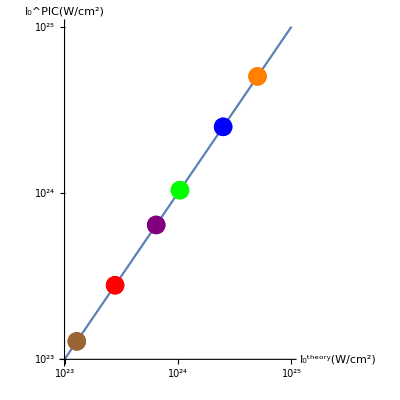

```mathematica
Clear[χe,ℰe,γe,Wγ,pc,tc,ω0,E0,ℰc,me,c,e,α,ℏ,T,ES,λμm,τ,I0,getI0]

me=9.11 10^-31;(*[Kg]*)
c= 299792458; (*[m/s]*)
e=1.602176634 10^-19; (*[C]*)
α=1/137; (*[]*)
ℏ=1.054571817 10^-34;(*[J s]*)
ES=me^2 c^3/(e ℏ);(*[V/m]*)
λμm=1;
ω0=2π c/(λμm 10^-6);
T=0.67(λμm 10^-6)/c;

getI0[ℰe_,τ_]:=Module[{I0,tc,tr,Wγ,E0,pr,ℰr,sol,γe,χe,eq},

χe=2γe E0/ES;
γe=ℰe/(me c^2);
Wγ=3^(2/3) 28 Gamma[2/3] α me^2 c^4χe^(2/3)  /(54 ℏ ℰe) ;
pr = Wγ tr;
tc=τ/(2Sqrt[2Log[2]]);
E0=0.855 λμm  Sqrt[I0 10^-18] me ω0 c/e;

(*tr definition a bit ambiguous in the text*)
tr=tc/Sqrt[2]  (Sqrt[2Log[2]])^(τ/T-1);

ℰr=(1-16/63)^pr  ℰe  //N//Simplify;

(*ℰr will be a function of I0 *)
eq=I0 10^-18== 2((ℰr/(me c^2))^2-1)/0.855^2;

(* solve numerically *)
sol=NSolve[eq,I0,Reals];
Return[sol[[1,1,2]]]
]

Show[{LogLogPlot[I0,{I0,10^23,10^25},AspectRatio->1,AxesLabel->{"I_0^theory(W/cm^2)","I_0^PIC(W/cm^2)"},ImageSize->400],ListLogLogPlot[getI0[6 10^9 e,T] Transpose[{{1},{1}}],PlotStyle->Directive[Blue,PointSize->0.1/3]],ListLogLogPlot[getI0[10 10^9 e,T] Transpose[{{1},{1}}],PlotStyle->Directive[Orange,PointSize->0.1/3]],ListLogLogPlot[getI0[30 10^9 e,3T] Transpose[{{1},{1}}],PlotStyle->Directive[Green,PointSize->0.1/3]],ListLogLogPlot[getI0[50 10^9 e,5T] Transpose[{{1},{1}}],PlotStyle->Directive[Red,PointSize->0.1/3]],ListLogLogPlot[getI0[100 10^9 e,5T] Transpose[{{1},{1}}],PlotStyle->Directive[Purple,PointSize->0.1/3]],ListLogLogPlot[getI0[100 10^9 e,7T] Transpose[{{1},{1}}],PlotStyle->Directive[Brown,PointSize->0.1/3]]}]
```

Figure 2
γmin=1/Sqrt[2 Δn]
In the limit χγ<<1 Δn=8α E0^2/(45 π ES^2)

Limit α χ^2/3 = 1 ( it needs to be multiplied by a factor of 2 to reproduce Fig4 )

```mathematica
Clear[χe,ℰe,γe,Wγ,pc,tc,ω0,E0,ℰc,me,c,e,α,ℏ,T,ES,λμm,τ,Δn]
χe=2γe E0/ES;
γe=ℰe/(me c^2);
ω0=2π c/(λμm 10^-6);
E0=0.855 λμm  Sqrt[I0 10^-18] me ω0 c/e;
ES=me^2 c^3/(e ℏ);(*[V/m]*)
Solve[χe==(1/α)^1.5,ℰe][[1,1,2]]
```

(93.0731 c^3 me^2 (1/α)^1.5)/(√I0 ℏ)

We need to invert the relation ℰ^c_e (ℰ_e) and replace ℰ^c_e by the corresponding γmin given by the Cherenkov condition

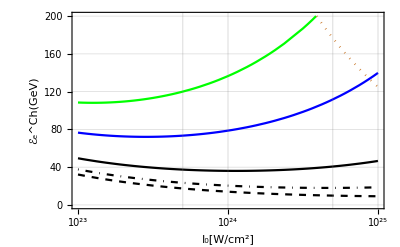

```mathematica
Clear[χe,ℰe,γe,Wγ,pc,tc,ω0,E0,ℰc,me,c,e,α,ℏ,T,ES,λμm,τ,Δn,getℰCh]

me=9.11 10^-31;(*[Kg]*)
c= 299792458; (*[m/s]*)
e=1.602176634 10^-19; (*[C]*)
α=1/137; (*[]*)
ℏ=1.054571817 10^-34;(*[J s]*)
ES=me^2 c^3/(e ℏ);(*[V/m]*)

getℰCh[I0_,τT_,λμm_]:=Module[{ℰCh,Δn,χe,γe,ℰe,pc,Wγ,tc,ω0,E0,T,τ},
χe=2γe E0/ES;
γe=ℰe/(me c^2);
Wγ=3^(2/3) 28 Gamma[2/3] α me^2 c^4χe^(2/3)  /(54 ℏ ℰe) ;
pc = Wγ tc;
tc=τ/(2Sqrt[2Log[2]]);
ω0=2π c/(λμm 10^-6);
E0=0.855 λμm  Sqrt[I0 10^-18] me ω0 c/e;
T=0.67(λμm 10^-6)/c;
τ=τT T;
Δn=8α E0^2/(45 π ES^2);
ℰCh=NSolve[ℰe(47/63)^((0.030199136711634034 c^4 me^2 ((√I0 ℰe)/(e ES))^(2/3) α τ)/(ℰe ℏ))==1/Sqrt[2 Δn]  me c^2,ℰe,Reals][[1,1,2]];
Return[ℰCh/(10^9 e)]
]

LogLinearPlot[ {getℰCh[I0,3,1],getℰCh[I0,2,1],getℰCh[I0,1,1],getℰCh[I0,1,0.5],getℰCh[I0,1,0.25],2(93.07306613561131 c^3 me^2 (1/α)^1.5)/(√I0 ℏ)/(10^9 e)},{I0,10^23,10^25},PlotPoints->2,PlotRange->{0,200},PlotStyle->{Directive[Green],Directive[Blue],Directive[Black],Directive[Black,DotDashed],Directive[Black,Dashed], Directive[Dotted],Directive[Darker[Yellow]],Directive[Yellow]},Frame->True,GridLines->Automatic,ImageSize->400,FrameLabel->{"I_0[W/cm^2]","ℰ_e^Ch(GeV)"}]
```